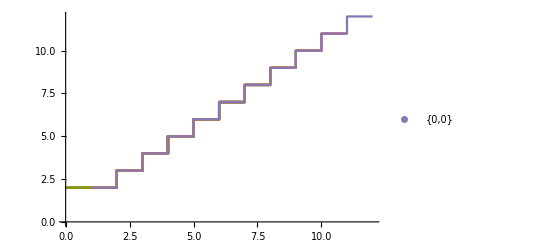
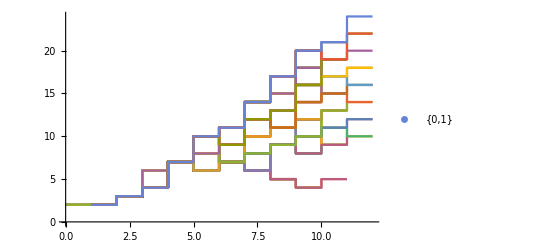
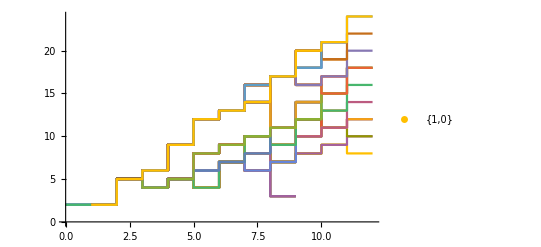
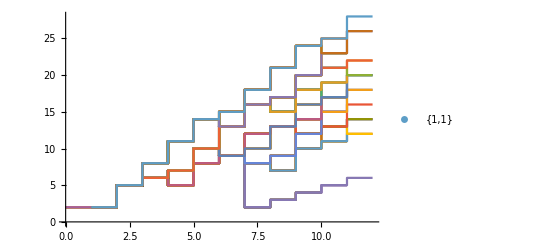
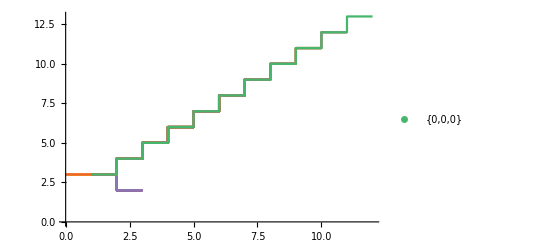
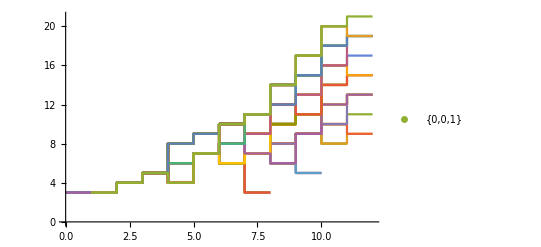
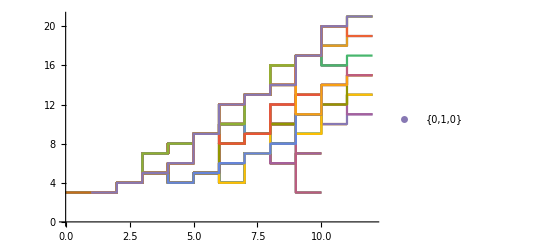
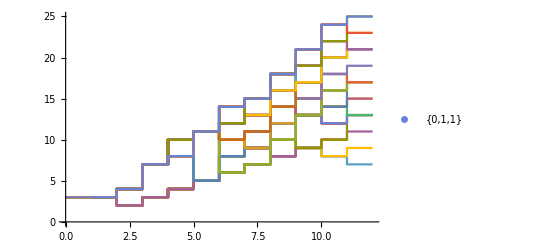

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
,allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
},
(*Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]*)
 (*Length /@allPaths[[-1]]*)
Table[
Length /@FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
]]]
lFn[l_,k_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
Table[ListStepPlot[Legended[FlattenAt[
 Table[
lFn[lengthInitialCondition,
indexInitialConditionWithGivenLength,
timeStep][[1]][[1]],
{timeStep,1,10}
]
,
{#}&/@Range[10]],Tuples[{0,1},lengthInitialCondition][[indexInitialConditionWithGivenLength]]]],
{lengthInitialCondition,2,3},
{indexInitialConditionWithGivenLength,1,2^lengthInitialCondition}]
```